```mathematica
(*** BID model with binomial partitioning ***)
```

```mathematica
(*** from part0-recurrences.nb we have the following BID solutions for the recurrence relations for h and z ***)
```

```mathematica
hsoln = (2^i l^n lp (-1+z) (λ+(-2+l) ν)+2^n l^i ((lp-(-2+l+lp) z) λ+(-2+l) ν))/(2^i (-1+l) l^n lp (-1+z) λ+2^n l^i ((lp-(-2+l+lp) z) λ+(-2+l) ν));
```

```mathematica
zsoln = (-2^i l (lp (-1+z) λ+(-2+l) (z λ-ν))+l^i lp (-1+z) (-2 ν+l (λ+ν)))/(2 (-1+l) l^i lp (-1+z) λ-2^i l (lp (-1+z) λ+(-2+l) (z λ-ν)));
```

```mathematica
(*** and for BID we have ***)
```

```mathematica
g[z_,t_]:=(-z λ+ν+ⅇ^(t (λ-ν)) (-1+z) ν)/(ⅇ^(t (λ-ν)) (-1+z) λ-z λ+ν)
```

```mathematica
ξ[z_,t_]:=((-λ+ν)/(ⅇ^(t (λ-ν)) (-1+z) λ-z λ+ν))^(α/λ)
```

```mathematica
(*** for binomial partitioning, φ[X,t] = 1 and θ[X,t] = 1/2 + X/2 ***)
```

```mathematica
(*** hence our generating function is Prod[ξ[z[i],t], {i, 1, n}] ξ[z,t] h0[z,t]^m0 ***)
```

```mathematica
(*** first, record h0[z,t]^m0 ***)
```

```mathematica
Gpart1=(hsoln/.i->0)^m0
```

((l^n lp (-1+z) (λ+(-2+l) ν)+2^n ((lp-(-2+l+lp) z) λ+(-2+l) ν))/((-1+l) l^n lp (-1+z) λ+2^n ((lp-(-2+l+lp) z) λ+(-2+l) ν)))^m0

```mathematica
(*** next address Prod[ξ[z[i],t], {i, 1, n}] ***)
```

```mathematica
pre1=FullSimplify[ξ[zsoln, τ]/.(λ-ν)^(2 i)->κ^i]
```

((2 (-1+l) l^i lp (-1+z) λ-2^i l (lp (-1+z) λ+(-2+l) (z λ-ν)))/(l^i (ⅇ^((λ-ν) τ) (-2+l)+l) lp (-1+z) λ+2^i l ((lp-(-2+l+lp) z) λ+(-2+l) ν)))^(α/λ)

```mathematica
(*** now split this into fractions so we can treat it ***)
```

```mathematica
numerator1=2 (-1+l) l^i lp (-1+z) λ-2^i l (lp (-1+z) λ+(-2+l) (z λ-ν));
denominator1=l^i (ⅇ^((λ-ν) τ) (-2+l)+l) lp (-1+z) λ+2^i l ((lp-(-2+l+lp) z) λ+(-2+l) ν);
```

```mathematica
(*** the fraction at the kernel of the product has a particular form which admits a solution for the overall product: ***)
```

```mathematica
Clear[A1, A2, B1, B2, a, b]
skeleton=Product[((A1 a^i +B1 b^i)/(A2 a^i + B2 b^i))^(α/λ) , {i, 1, n}]
```

((B1^(1+n) B2^(-1-n) (A2+B2) QPochhammer[-A1/B1,a/b,1+n])/((A1+B1) QPochhammer[-A2/B2,a/b,1+n]))^(α/λ)

```mathematica
(*** with appropriate choices of a and b we can force the numerator and denominator into the required forms ***)
```

```mathematica
zsoln
```

(-2^i l (lp (-1+z) λ+(-2+l) (z λ-ν))+l^i lp (-1+z) (-2 ν+l (λ+ν)))/(2 (-1+l) l^i lp (-1+z) λ-2^i l (lp (-1+z) λ+(-2+l) (z λ-ν)))

```mathematica
At1 =  lp (-xtwo)^2 (z-1)(λ-ν);
Bt1 =2 xone^n (ν-λ z);
At2 = 2lp (-xtwo)^n ν(z-1);
Bt2 = 2 xone^n (ν-λ z);
```

```mathematica
tmpA1=Simplify[At2(ν-λ)]
tmpB1 = Simplify[Bt2(ν-λ)]
tmpA2 =Simplify[λ l (At1-At2) + ν At2 - λ At1]
tmpB2=Simplify[λ l (Bt1-Bt2) + ν Bt2 - λ Bt1]
```

2 lp (-xtwo)^n (-1+z) ν (-λ+ν)

2 xone^n (-λ+ν) (-z λ+ν)

2 lp (-1+z) ((-1+l) xtwo^2 λ (λ-ν)-(-xtwo)^n (l λ-ν) ν)

2 xone^n (λ-ν) (z λ-ν)

```mathematica
A1 = FullSimplify[Coefficient[numerator1, l^i]]
B1= FullSimplify[Coefficient[numerator1, 2^i ]]
A2 = FullSimplify[Coefficient[denominator1,l^i]/.ⅇ^((λ-ν) τ)->l]
B2= FullSimplify[Coefficient[denominator1, 2^i]]
```

2 (-1+l) lp (-1+z) λ

l (lp (λ-z λ)-(-2+l) (z λ-ν))

(-1+l) l lp (-1+z) λ

l (lp (λ-z λ)-(-2+l) (z λ-ν))

```mathematica
(*** we then have an expression for the product, and combined with ξ[z,t] we have the remaining part of our generating function ***)
```

```mathematica
Simplify[((l (-2+l)+l) lp (-1+z) λ+l (lp (λ-z λ)-(-2+l) (z λ-ν))) ]
```

(-2+l) l (lp (-1+z) λ-z λ+ν)

```mathematica
Gpart2=(skeleton*ξ[z, t])/.a->e2/.b->2(-e1)/.e1-> ((-1+ⅇ^((-λ+ν) τ)) λ)/(λ-ν)/.e2-> ((-1+ⅇ^((λ-ν) τ)) λ)/(λ-ν)
```

((-λ+ν)/(ⅇ^(t (λ-ν)) (-1+z) λ-z λ+ν))^(α/λ) ((((ⅇ^((λ-ν) τ) (-2+l)+l) lp (-1+z) λ+l (lp (λ-z λ)-(-2+l) (z λ-ν))) QPochhammer[-(2 (-1+l) lp (-1+z) λ)/(l (lp (λ-z λ)-(-2+l) (z λ-ν))),-(-1+ⅇ^((λ-ν) τ))/(2 (-1+ⅇ^((-λ+ν) τ))),1+n])/((2 (-1+l) lp (-1+z) λ+l (lp (λ-z λ)-(-2+l) (z λ-ν))) QPochhammer[-((ⅇ^((λ-ν) τ) (-2+l)+l) lp (-1+z) λ)/(l (lp (λ-z λ)-(-2+l) (z λ-ν))),-(-1+ⅇ^((λ-ν) τ))/(2 (-1+ⅇ^((-λ+ν) τ))),1+n]))^(α/λ)

```mathematica
Gpart2=Simplify[(skeleton*ξ[z, t])/.a->e2/.b->2(-e1)]/.e1-> ((-1+ⅇ^((-λ+ν) τ)) λ)/(λ-ν)/.e2-> ((-1+ⅇ^((λ-ν) τ)) λ)/(λ-ν)
```

((-λ+ν)/(ⅇ^(t (λ-ν)) (-1+z) λ-z λ+ν))^(α/λ) (((ⅇ^((λ-ν) τ) lp (-1+z) λ+l (-z λ+ν)) QPochhammer[(2 (-1+l) lp (-1+z) λ)/(l (lp (-1+z) λ+(-2+l) (z λ-ν))),-(-1+ⅇ^((λ-ν) τ))/(2 (-1+ⅇ^((-λ+ν) τ))),1+n])/((lp (-1+z) λ+l (-z λ+ν)) QPochhammer[((ⅇ^((λ-ν) τ) (-2+l)+l) lp (-1+z) λ)/(l (lp (-1+z) λ+(-2+l) (z λ-ν))),-(-1+ⅇ^((λ-ν) τ))/(2 (-1+ⅇ^((-λ+ν) τ))),1+n]))^(α/λ)

```mathematica
(*** so the complete generating function is ***)
```

```mathematica
Gfinal=Simplify[Gpart1*Gpart2];
FullSimplify[Gfinal]
```

((-λ+ν)/(ⅇ^(t (λ-ν)) (-1+z) λ-z λ+ν))^(α/λ) ((l^n lp (-1+z) (λ+(-2+l) ν)+2^n ((lp-(-2+l+lp) z) λ+(-2+l) ν))/((-1+l) l^n lp (-1+z) λ+2^n ((lp-(-2+l+lp) z) λ+(-2+l) ν)))^m0 (((ⅇ^((λ-ν) τ) lp (-1+z) λ+l (-z λ+ν)) QPochhammer[(2 (-1+l) lp (-1+z) λ)/(l (lp (-1+z) λ+(-2+l) (z λ-ν))),1/2 ⅇ^((λ-ν) τ),1+n])/((lp (-1+z) λ+l (-z λ+ν)) QPochhammer[((ⅇ^((λ-ν) τ) (-2+l)+l) lp (-1+z) λ)/(l (lp (-1+z) λ+(-2+l) (z λ-ν))),1/2 ⅇ^((λ-ν) τ),1+n]))^(α/λ)

```mathematica
(*** we can now compute statistics and compare with stochastic simulation ***)
```

```mathematica
dg1 = Simplify[D[Gfinal,z]/.z->1];
dg2 =Simplify[D[Gfinal,{z,2}]/.z->1];
```

```mathematica
numsubsa = {α ->0.2, λ->0.06,ν->0.01, τ->10, m0->100}
```

{α→0.2,λ→0.06,ν→0.01,τ→10,m0→100}

```mathematica
mean = dg1/.l->Exp[(λ-ν)τ]/.lp->Exp[(λ-ν)t]/.κ->(λ-ν)^2;
variance = (dg2+dg1-dg1^2)/.l->Exp[(λ-ν)τ]/.lp->Exp[(λ-ν)t]/.κ->(λ-ν)^2;
zero = Gfinal/.z->0/.l->Exp[(λ-ν)τ]/.lp->Exp[(λ-ν)t]/.κ->(λ-ν)^2;
```

```mathematica
meantaba=Table[{tt,mean/.n->Floor[tt/τ]/.t->tt-τ*Floor[tt/τ]/.numsubsa, variance/.n->Floor[tt/τ]/.t->tt-τ*Floor[tt/τ]/.numsubsa}, {tt, 0, 200}];
```

```mathematica
p1 = Table[{meantaba[[i]][[1]], meantaba[[i]][[2]]}, {i, 1, Length[meantaba]}];
p2 = Table[{meantaba[[i]][[1]], meantaba[[i]][[3]]}, {i, 1, Length[meantaba]}];
```

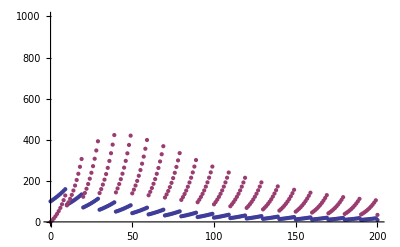

```mathematica
ListPlot[{p1, p2}, PlotRange->{0, 1000}]
```

```mathematica
Export["testtheorya.dat", meantaba]
```